/Users/xisanboshi/Desktop/TITS.R2/time/testset

Importing data from /Users/xisanboshi/Desktop/TITS.R2/time/testset

Importing Finish

{4.55113,Null}

{124.449,Null}

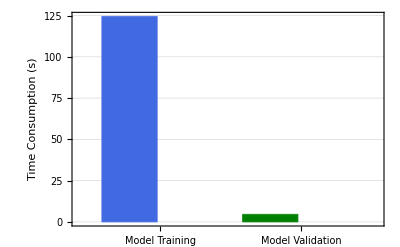

```mathematica
ClearAll["`*"];
rootDir=NotebookDirectory[];
recordNum=1;
teSet=rootDir<>"testset"
testVehicleNum=1;
recordNum=1;
getVehicleRecord[]:=Module[{
dir=teSet,
record,
recOut,recIn},
Print["Importing data from "<>dir];
record=Import[FileNameJoin[{dir,"airsim_rec.txt"}],
"Table"]//Rest;
Print["Importing Finish"];
recOut=Map[#[[{10}]]&,record];
recIn=Map[Import[FileNameJoin[{
dir,"images",Last[#]}]]&,
record];
{Thread[recIn->recOut]}
];
neuralNetStruct={
ConvolutionLayer[20,5],
Ramp,PoolingLayer[2,2],
ConvolutionLayer[50,5],
Ramp,
PoolingLayer[2,2],
FlattenLayer[],
300,
Ramp,
1};
setLayers={1,4,8,10};
getNet[]:=NetChain[neuralNetStruct,
"Output"->1,
"Input"->NetEncoder[
{"Image",{144,256},"RGB"}]]//NetInitialize;


getPath[i_]:=FileNameJoin[{NotebookDirectory[],"local-"<>
ToString[i]<>".wlnet"}];

(*Loading testing dataset for model validation*)
testVehicleNum=1;
{record}=getVehicleRecord[];
realmove=Values[record];
inputpic=Keys[record];
maeResult={};

netR=Import[getPath[1]];
(*Obtaining Time consumption*)
validationDelay=AbsoluteTiming[crtl2=netR[inputpic];
offset=Abs[crtl2-realmove];
mae=Total[offset]/Length[offset];]

(*Training the data*)
trainData=record;
(*Obtaining the Time Consumption*)
trainTime=AbsoluteTiming[net=NetTrain[getNet[],trainData, Method->{"SignSGD","LearningRate"->0.001},
TrainingProgressReporting->
File[FileNameJoin[{NotebookDirectory[],
"train_out-1.csv"}]]];]
BarChart[{Style[trainTime,RGBColor[0.2549,0.4118,0.8824]],Style[validationDelay,RGBColor[0,0.5020,0]]},ChartLabels->{{"Model Training","Model Validation"},None},GridLines->Automatic,Frame->True,FrameLabel->{,"Time Consumption (s)"},PlotTheme->"Scientific"]
```